# 3T Modelling Thermodynamics and Equilibrium of mixture of radiation field, ionic gas and electron gas

## Constants and Functions

electron-ion collision cross sections
typically 10^(-11) m^2
https://www.nist.gov/system/files/documents/srd/jpcrd386.pdf

```mathematica
(* Initial parameters and constants *)

c = 3.0*10^(8)
ep0 = 8.8541878128*10^(−12);
kb = 1.380649*10^(−23);
ee = 1.602*10^(-19);

a = 2*10^(-10);
mp = 1.67262192*10^(-27);
hbar = 1.05457182 *10^(-34);
me = 9.1093837*10^(-31);
ui = 13.6 * ee;(* ionization energy for hydrogen*)

ar = 5.670374*10^(-8) ;(* stefan-boltzmann constant *)

sigmaie = 1.0*10^(-11); (* e- ion collision cross section  m^2*)
sigmaii  = Pi*a*a; (* ion ion collision cross section based on atomic size *)
```

3.×10^8

```mathematica
(* Saha equation*) (* Here calculate the ionization fraction *)
x[N_,T_, Ne_]:= ((2*Pi*me*kb/hbar)^(3/2))*(T^(3/2)/Ne)*Exp[-(ui/(kb*T))]; (* Ne is electron number density *) (* typical ne 10^(-20)*)

(* time between collisions ... relaxation time*)
taun[N_,T_]:=(1/(N*sigmaii))*Sqrt[mp/(kb*T)];
taue[Ne_,Te_]:=(1/(Ne*sigmaie))*Sqrt[me/(kb*Te)]
```

## Radiation and Perfect Gas

and Gas Perfect Radiation

```mathematica
pr[N_, Vo_, T_]:= (N*kb*T/Vo)+(ar*T^4)/3;
Et[N_,Vo_,T_]:= (3/2)*(N*kb*T)+(Vo*ar*T^4);
St[N_,Vo_,T_]:= N*kb*Log[Vo*T^(3/2)]+(4/3)*ar*Vo*T^3
```

## Radiation and Ionic Gas

```mathematica
(*   using saha equation  to get energy and pressure for ionic gas and radiation field*)
```

## Planck and Bose Einstein Distribution

```mathematica
(*  Planck distribution*)
```

```mathematica
npl[nu_,T_]:= 1.0/(Exp[2*Pi*hbar*nu/(kb*T)]-1.0)
```

```mathematica
(* Bose-Einstein distribution*)
```

```mathematica
nbe[nu_,mu_,T_]:= 1.0/(Exp[((2*Pi*hbar*nu)/(kb*T))-mu]-1.0)
```

## Experiments

```mathematica
2*Pi*hbar/kb
```

4.79924×10^-11

3.×10^17

{1./(-1.+ⅇ^(-0.005+(1.43977×10^7)/T)),1./(-1.+ⅇ^(-0.1+(1.43977×10^7)/T)),1./(-1.+ⅇ^(-0.2+(1.43977×10^7)/T)),1./(-1.+ⅇ^(-0.3+(1.43977×10^7)/T))}

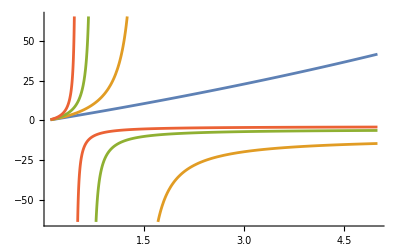

```mathematica
nur = 3.0*10^(17)
myl={nbe[nur,0.005,T], nbe[nur,0.1,T]   ,   nbe[nur,0.2,T] ,   nbe[nur,0.3,T]}
Plot[myl,{T,10*10^6,500*10^6}]
```

```mathematica
{X,Y}={x,y}/. DSolve[{x'[t]==-c1*x[t]/c2+c1*(y[t]-x[t])/c2,y'[t]==-c1*(y[t]-x[t])/c2,x[0]==0,y[0]==1},{x,y},t]//FullSimplify//First
```

{Function[{t},(ⅇ^(-(3 c1 t)/(2 c2)-(√5 c1 t)/(2 c2)) (-1+ⅇ^((√5 c1 t)/c2)))/(√5)],Function[{t},1/10 ⅇ^(-(3 c1 t)/(2 c2)-(√5 c1 t)/(2 c2)) (5-√5+5 ⅇ^((√5 c1 t)/c2)+√5 ⅇ^((√5 c1 t)/c2))]}

```mathematica
Manipulate[Plot[Evaluate[{X[t],Y[t]}/. {c1->a,c2->b}],{t,0,10},PlotRange->{0,1},PlotStyle->Thick,Filling->{1->{2}}],{{a,1.3,"c1"},1,3,Appearance->"Labeled"},{{b,2.5,"c2"},1,3,Appearance->"Labeled"}]
```